```mathematica
M=50;XX=({{a}, {b}, {c}, {d}});
```

```mathematica
Coeff=Table[({{0}, {0}, {0}, {0}}),{i,0,M},{j,0,9},{k,0,2}];
Coeff[[2,1,1]]=({{0}, {1}, {0}, {0}});Coeff[[1,2,1]]=({{0}, {0}, {1}, {0}});Coeff[[1,1,2]]=({{0}, {0}, {0}, {1}});
```

```mathematica
Coeff[[2,1,1]]
```

{{0},{1},{0},{0}}

### Removing Resonances

```mathematica
f[c0_,c1_,c2_,c3_]:=({{c0^2+2 c1^2+2 c2^2+2 c3^2}, {-c1+2 c0 c1+2 c1 c2+2c3 c2}, {-4c2 +2 c0 c2+c1^2+2c3 c1}, {-9 c3 +2 c0 c3+2  c1 c2}})
F[P_]:=f[P[[1]],P[[2]],P[[3]],P[[4]]]
P[θ1_,θ2_,θ3_]:=Sum[Coeff[[i+1,j+1,k+1]]If[i==0,1,θ1^i]If[j==0,1,θ2^j]If[k==0,1,θ3^k],{i,0,M},{j,0,9},{k,0,2}]
```

```mathematica
Coeff[[1+6,1+1,1]]
```

{{2669/7200},{0},{5951/5184},{0}}

```mathematica
Clear[β,δ,α,γ]
```

```mathematica
p=30;q=0;
Coeff[[1+p,1+q,1]]=XX
γ=1;
α=1;
δ=19/24;
β=11/81


h[θ1_,θ2_,θ3_]:=({{-θ1}, {-4 θ2+α 1/3 θ1^4}, {-9θ3+β θ1^9-γ θ1 θ2^2+δ θ1^5 θ2^1}})


JacP[θ1_,θ2_,θ3_]=Table[{
D[P[θ1,θ2,θ3],θ1][[i,1]],
D[P[θ1,θ2,θ3],θ2][[i,1]],
D[P[θ1,θ2,θ3],θ3][[i,1]]},{i,1,4}];

xx=Simplify[Flatten[F[P[θ1,θ2,θ3]]- JacP[θ1,θ2,θ3].h[θ1,θ2,θ3]]];
Collect[xx,θ1]//MatrixForm;
xx//MatrixForm;
Collect[Series[xx/.θ3->0,{θ1,0,10},{θ2,0,0}]//Simplify,θ2]//MatrixForm;
Collect[Series[xx/.θ1->0/.θ2->0,{θ3,0,6},{θ2,0,2}]//Simplify,θ3]//MatrixForm;
Series[xx,{θ3,0,6},{θ2,0,6},{θ3,0,0}]//MatrixForm;

reduce=Normal[Series[xx,{θ1,0,p},{θ2,0,q},{θ3,0,0}]]
sol=Solve[1/(θ1^p θ2^q)reduce=={0,0,0,0},{a,b,c,d}]
Coeff[[1+p,1+q,1]]=Evaluate[XX/.sol][[1]]
```

{{a},{b},{c},{d}}

11/81

{((21157019334572477001541094216609048903+95267468528664444216646041600000000000 a) θ1^30)/3175582284288814807221534720000000000,29 b θ1^30,((38712019382595773104457328377404752167+206412848478772962469399756800000000000 c) θ1^30)/7938955710722037018053836800000000000,21 d θ1^30}

{{a→-21157019334572477001541094216609048903/95267468528664444216646041600000000000,b→0,c→-38712019382595773104457328377404752167/206412848478772962469399756800000000000,d→0}}

{{-21157019334572477001541094216609048903/95267468528664444216646041600000000000},{0},{-38712019382595773104457328377404752167/206412848478772962469399756800000000000},{0}}

```mathematica
Coeff[[1+p,1+q,1]]=Evaluate[XX/.sol][[1]]
```

{{-5034896237/11197440000},{0},{-333794429/1866240000},{0}}

```mathematica
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,0,0}]
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,1,1}]
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,2,2}]
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,3,3}]
```

{{(0
0
0
0)},{(0
1
0
0)},{(-1
0
1/2
0)},{(0
1/2
0
1/6)},{(-7/8
0
0
0)},{(0
23/48
0
0)},{(-19/27
0
-1/12
0)},{(0
43/96
0
-11/96)},{(-8119/13824
0
-193/1728
0)},{(0
22999/55296
0
0)},{(-1728521/3456000
0
-234733/1492992
0)},{(0
691754011/1866240000
0
-465079/2985984)},{(-5034896237/11197440000
0
-333794429/1866240000
0)},{(0
51249768353/134369280000
0
4127903/829440000)},{(-95209060531/235146240000
0
-34366782377/167961600000
0)},{(0
839125235131/2438553600000
0
187709801791/4031078400000)},{(-311394393169217/842764124160000
0
-20832683582611/98761420800000
0)},{(0
32221372165790779/101131694899200000
0
14316007393367/175575859200000)},{(-22328677540266613/65013232435200000
0
-151194761747242043/707921864294400000
0)},{(0
3781465683809211359/12742593557299200000
0
245810900353185931/2359739547648000000)},{(-21462082965959968453/68263894056960000000
0
-27047819280853166303/127425935572992000000
0)},{(0
10573766090655465355547/38227780671897600000000
0
16999240432185570511/143354177519616000000)},{(-176338879259426823299/600722267701248000000
0
-1807016925590823572471/8601250651176960000000
0)},{(0
266987976824906735241821/1027902546955468800000000
0
67897534566696014649061/535188929406566400000000)},{(-541869341904630616606020187/1998242551281431347200000000
0
-1195349404249665176006729261/5828207441237508096000000000
0)},{(0
136734931989622776417496971737/559507914358800777216000000000
0
254427874385296134400218881/1942735813745836032000000000)},{(-2650390658327099364955769333/10490773394227514572800000000
0
-230783922942918453042898610851/1153985073365026603008000000000
0)},{(0
273793001775936746215494773273/1185327877826792757657600000000
0
8795663101329387122291402435959/66469540225825532333260800000000)},{(-120308697695960439320124931496171/509152202066508707266560000000000
0
-5029646320216514830140649744449961/25923120688071957609971712000000000
0)},{(0
5561220863659695105207159495178437199/25404658274310518457772277760000000000
0
170531459188482004753468578692239997/1296156034403597880498585600000000000)},{(-21157019334572477001541094216609048903/95267468528664444216646041600000000000
0
-38712019382595773104457328377404752167/206412848478772962469399756800000000000
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)}}

{{(0
0
1
0)},{(0
-1/2
0
1/2)},{(0
0
1
0)},{(0
-13/18
0
3/4)},{(25/144
0
139/144
0)},{(0
-55/64
0
0)},{(2669/7200
0
5951/5184
0)},{(0
-1159909/1296000
0
-12343/10368)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)}}

{{(-1/4
0
0
0)},{(0
1/16
0
0)},{(-23/40
0
1/16
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)}}

{{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)},{(0
0
0
0)}}

## Special

```mathematica
Coeff[[5,1,1]]={{-7/8},{0},{0},{0}}
```

{{-7/8},{0},{0},{0}}

```mathematica
Coeff[[2,3,1]]={{0},{1/16},{0},{0}}
```

{{0},{1/16},{0},{0}}

```mathematica
Coeff[[6,2,1]]={{0},{-55/64},{0},{0}}
```

{{0},{-55/64},{0},{0}}

```mathematica
Coeff[[10,1,1]]={{0},{22999/55296},{0},{0}}
```

{{0},{22999/55296},{0},{0}}

```mathematica
1+p
1+q
```

6

2

```mathematica
-55/64
```

```mathematica
p
```

4

```mathematica
24/6//Simplify
```

4

```mathematica
({{4, 0, 0, 0}, {0, 3, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, -5}}).({{a}, {b}, {c}, {d}})
```

{{4 a},{3 b},{0},{-5 d}}

```mathematica
ζ=({{0}, {0}, {1}, {0}})
```

{{0},{0},{1},{0}}

```mathematica
Coeff[[7,1,1]]
```

{{0},{0},{0},{0}}

{{0},{1/16},{0},{DD}}

{{-7/8},{0},{CC},{0}}

```mathematica
ParametricPlot3D[Table[P[θ1,- 1/6 Log[θ1^2] θ1^4+θ2,245/(2 648)Log[θ1^2] θ1^9][[i]],{i,1,3}],{θ1,-.8,.8},{θ2,-.3,.3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Table[P[θ1,- 1/6 Log[θ1^2] θ1^4+θ2,245/(2 648)Log[θ1^2] θ1^9][[i]],{i,1,3}],{θ1,-1,1},{θ2,-.3,.3}]
```

```mathematica
ParametricPlot3D[Table[P[θ1,- 1/6 Log[θ1^2] θ1^4+θ2,245/(2 648)Log[θ1^2] θ1^9][[i]],{i,1,3}],{θ1,-1,1},{θ2,-.3,.3}]
```

$Aborted

```mathematica
P[θ1,0,0][[2]]
```

{θ1+θ1^3/2+(23 θ1^5)/48+(43 θ1^7)/96+(22999 θ1^9)/55296}

```mathematica
ParametricPlot3D[{P[θ1,θ2,0][[1]],P[θ1,θ2,0][[2]],P[θ1,θ2,0][[3]]},{θ1,-1,1},{θ2,-1,1}]
```

-Graphics3D-

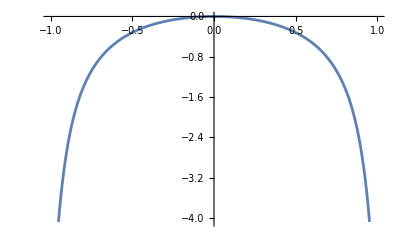

```mathematica
Plot[P[θ1,0,0][[1]],{θ1,-1,1}]
```

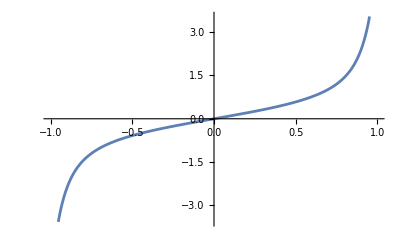

```mathematica
Plot[P[θ1,0,0][[2]],{θ1,-1,1}]
```

```mathematica
F[a0_,a1_,a2_,a3_]:={ a0^2+2(a1^2+a2^2 +a3^2),-1a1+ (2 a2 a1+  2 a3 a2) +  2 a0 a1,  -2^2 a2+(a1 a1+ (2 a3 a1) )+  2 a0  a2,  3^2 a3 +(2 a1 a2 )+   2 a0 a3}
```

```mathematica
θ1o=.2;
θ2o=0;
θ3o=0;
A0O=P[θ1o,θ2o,θ3o][[1]];
A1O=P[θ1o,θ2o,θ3o][[2]];
A2O=P[θ1o,θ2o,θ3o][[3]];
A3O=P[θ1o,θ2o,θ3o][[4]];

Tmax=5000;
sol=NDSolve[{{a0'[t],a1'[t],a2'[t],a3'[t]}== I F[a0[t],a1[t],a2[t],a3[t]],
{a0[0],a1[0],a2[0],a3[0]}== {A0O,A1O,A2O,A3O}
},
{a0,a1,a2,a3},{t,0,Tmax},AccuracyGoal->15,PrecisionGoal->12];
```

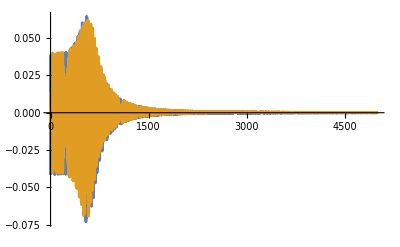

```mathematica
Plot[Evaluate[{Re[a0[t]],Im[a0[t]]}/.sol],{t,0,Tmax},PlotRange->All]
```

```mathematica
g0=Plot[Evaluate[{Abs[a0[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];
g1=Plot[Evaluate[{,Abs[a1[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];g2=Plot[Evaluate[{,,Abs[a2[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];g3=Plot[Evaluate[{,,,Abs[a3[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];
```

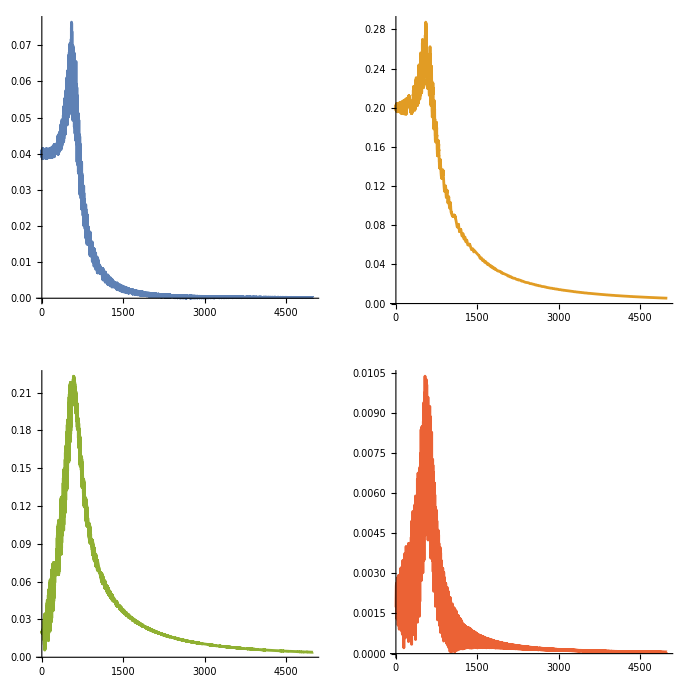

```mathematica
GraphicsGrid[{{g0,g1},{g2,g3}}]
```

## Analytic Functions

```mathematica
DSolve[I{θ1'[t],θ2'[t],θ3'[t]}==Flatten[h[θ1[t],θ2[t],θ3[t]]],{θ1,θ2,θ3},t]//Simplify
```

{{θ1→Function[{t},ⅇ^(ⅈ t) C[1]],θ2→Function[{t},-1/3 ⅈ ⅇ^(4 ⅈ t) t C[1]^4+ⅇ^(4 ⅈ t) C[2]],θ3→Function[{t},-1/648 ⅈ ⅇ^(9 ⅈ t) (88 t C[1]^9-171/2 ⅈ t^2 C[1]^9+24 t^3 C[1]^9+513 t C[1]^5 C[2]+216 ⅈ t^2 C[1]^5 C[2]-648 t C[1] C[2]^2)+ⅇ^(9 ⅈ t) C[3]]}}

```mathematica
(-1/648 ⅈ ⅇ^(9 ⅈ t) (88 t C[1]^9-171/2 ⅈ t^2 C[1]^9+24 t^3 C[1]^9+513 t C[1]^5 C[2]+216 ⅈ t^2 C[1]^5 C[2]-648 t C[1] C[2]^2)+ⅇ^(9 ⅈ t) C[3])/ⅇ^(9 ⅈ t)//Expand
```

-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9-19/24 ⅈ t C[1]^5 C[2]+1/3 t^2 C[1]^5 C[2]+ⅈ t C[1] C[2]^2+C[3]

```mathematica
Simplify[-19/24 ⅈ t C[1]^5 C[2]+1/3 t^2 C[1]^5 C[2]]
```

```mathematica
Expand[1/24 t (-19 ⅈ+8 t) ]
```

```mathematica
TeXForm[-(19 ⅈ t)/24+t^2/3]
```

\frac{t^2}{3}-\frac{19 i t}{24}

```mathematica
Expand[-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9]
```

```mathematica
Expand[(-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9)/C[1]^9]
```

```mathematica
TeXForm[-(-(11 ⅈ t)/81-(19 t^2)/144-(ⅈ t^3)/27)]
```

\frac{i t^3}{27}+\frac{19 t^2}{144}+\frac{11 i t}{81}